Delta+Kernel

```mathematica
f[t_]= DiracDelta[t]/2+Exp[-Abs[t]/τP]/(2τP);
```

```mathematica
InverseLaplaceTransform[(γ LaplaceTransform[f[t],t,s]x0)/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

1/(2 √(γ^2+τP^2 ω0^4))x0 (-ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2-ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))

```mathematica
InverseLaplaceTransform[1/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

1/(γ √(γ^2+τP^2 ω0^4))(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2-ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4))

```mathematica
f1[t_]=1/(2 √(γ^2+τP^2 ω0^4))x0 (-ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) γ+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2-ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^2+ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4)+ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) √(γ^2+τP^2 ω0^4));
```

```mathematica
Aux[t_]=ω0^4/(kB T)Expand[(f1[t])(x0)];
Aux2[t_]=Expand[Aux[t]/.{x0^2->(kB T)/ω0^2,x0->λ0}]
```

1/2 ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) ω0^2+1/2 ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) ω0^2-(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4))-(ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4))

```mathematica
Cte=Limit[Aux2[t],t->Infinity]
```

ConditionalExpression[0, γ τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))>0]

```mathematica
Psi[t_]=Aux2[Abs[t]]-Cte
```

ConditionalExpression[1/2 ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) ω0^2+1/2 ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) ω0^2-(ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4))-(ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4)), γ τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))>0]

```mathematica
Assuming[{γ>0,ω0>0,τP>0,λ0>0},FourierTransform[Psi[t],t,ω]]
```

ConditionalExpression[(2 √(2/π) γ (2+τP^2 ω^2) ω0^4)/(γ^2 ω^2 (4+τP^2 ω^2)+4 γ τP ω^2 ω0^2+4 (1+τP^2 ω^2) ω0^4), γ τP (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))>0]

```mathematica
Assuming[{γ>0,ω0>0,τP>0,λ0>0},Integrate[Psi[t]/Psi[0],{t,0,Infinity}]]
```

ConditionalExpression[γ/ω0^2, ]

```mathematica
Assuming[γ>0,Limit[Psi[t],τP->0,Direction->"FromAbove"]]
```

ⅇ^(-(ω0^2 Abs[t])/γ) ω0^2

Delta+Delta

```mathematica
f[t_]=2 DiracDelta[t]/2;
```

```mathematica
InverseLaplaceTransform[(γ LaplaceTransform[f[t],t,s]x0)/(ω0^2+γ s LaplaceTransform[f[t],t,s]),s,t]
```

ⅇ^(-(t ω0^2)/γ) x0

```mathematica
f1[t_]=ⅇ^(-(t ω0^2)/γ) x0;
Aux[t_]=ω0^4/(kB T)Expand[(f1[t]-λ0)(x0-λ0)]
```

((ⅇ^(-(t ω0^2)/γ) x0^2-x0 λ0-ⅇ^(-(t ω0^2)/γ) x0 λ0+λ0^2) ω0^4)/(kB T)

```mathematica
Aux2[t_]=Aux[t]/.{x0^2->(kB T)/ω0^2,x0->λ0}
```

((-ⅇ^(-(t ω0^2)/γ) λ0^2+(ⅇ^(-(t ω0^2)/γ) kB T)/ω0^2) ω0^4)/(kB T)

```mathematica
Limit[Aux2[t],t->Infinity]
```

ConditionalExpression[0, (1/kB|1/T|λ0^2|kB|T)∈ℝ&&γ ω0^2>0]

```mathematica
Psi[t_]=Simplify[Aux2[Abs[t]]]
```

(ⅇ^(-(ω0^2 Abs[t])/γ) ω0^2 (kB T-λ0^2 ω0^2))/(kB T)

```mathematica
Integrate[Psi[t]/Psi[0],{t,0,Infinity}]
```

Piecewise[{{γ/ω0^2, Re[ω0^2/γ]>0}, {Integrate[(-ⅇ^(-(ω0^2 Abs[t])/γ) λ0^2+(ⅇ^(-(ω0^2 Abs[t])/γ) kB T)/ω0^2)/(-λ0^2+(kB T)/ω0^2),{t,0,∞},Assumptions→Re[ω0^2/γ]≤0], True}}]

```mathematica
Assuming[γ>0,Limit[Psi[t],τP->0,Direction->"FromAbove"]]
```

ⅇ^(-(ω0^2 Abs[t])/γ) ω0^2

Optimal protocol

```mathematica
Aux3[t_]=1/2 ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) ω0^2+1/2 ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) ω0^2-(ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^((-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4))-(ⅇ^((-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP)) Abs[t]) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4));
Psi[t]=Aux3[t]/Aux3[0];
```

```mathematica
Integrate[Psi[t],{t,0,Infinity}]
```

$Aborted

```mathematica
Simplify[LaplaceTransform[Psi[t],t,s]/.s->0]
```

γ/ω0^2

```mathematica
dPsi[t_]=D[Psi[t],t]/. Abs'[t]->Sign[t];
```

```mathematica
ddPsi[t_]=D[dPsi[t],t]/. {Abs'[t]->Sign[t],Sign'[t]->2DiracDelta[t]};
```

```mathematica
Integrate[ddPsi[t]Exp[-s t],{t,0,Infinity}]/.HeavisideTheta[0]->1/2
```

ConditionalExpression[-(2 s (1+s τP) ω0^2)/(s γ (2+s τP)+2 (1+s τP) ω0^2), ]

```mathematica
Simplify[LaplaceTransform[ddPsi[t],t,s]]
```

-(2 ω0^2 (3 s γ+2 s^2 γ τP+2 ω0^2+2 s τP ω0^2))/(γ (s^2 γ τP+2 ω0^2+2 s (γ+τP ω0^2)))

```mathematica
Series[1/(s (-(2 s (1+s τP) ω0^2)/(s γ (2+s τP)+2 (1+s τP) ω0^2))),{s,0,3}]
```

-1/s^2-γ/(ω0^2 s)+(γ τP)/(2 ω0^2)-((γ τP^2) s)/(2 ω0^2)+(γ τP^3 s^2)/(2 ω0^2)-((γ τP^4) s^3)/(2 ω0^2)+O[s]^4

-1/s^2-γ/(ω0^2 s)+(γ τP)/(2 ω0^2)-((γ τP^2) s)/(2 ω0^2)+O[s]^2

Optimal work

```mathematica
Clear[γ,ω0,τP]
```

```mathematica
Psi[t_]=1/2 ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) ω0^2+1/2 ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) ω0^2-(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) γ ω0^2)/(2 √(γ^2+τP^2 ω0^4))+(ⅇ^(t (-1/τP-ω0^2/γ-(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4))-(ⅇ^(t (-1/τP-ω0^2/γ+(√(γ^2+τP^2 ω0^4))/(γ τP))) τP ω0^4)/(2 √(γ^2+τP^2 ω0^4));
```

```mathematica
p[t_]=1/τ;
popt[t_]=1/(τ+2γ/ω0^2)+2(γ/ω0^2)/(τ+2γ/ω0^2)(DiracDelta[t]+DiracDelta[τ-t]);
```

```mathematica
Aux5[τ_]=Assuming[{γ>0,ω0>0,τP>0},Integrate[Psi[t-u],{t,0,τ},{u,0,t}]]
```

1/2 γ (2 τ+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))+((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))-((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))

```mathematica
Expand[popt[t]popt[u]]
```

1/((τ+(2 γ)/ω0^2)^2)+(2 γ DiracDelta[t])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(2 γ DiracDelta[u])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(4 γ^2 DiracDelta[t] DiracDelta[u])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(2 γ DiracDelta[-t+τ])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(4 γ^2 DiracDelta[u] DiracDelta[-t+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(2 γ DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(4 γ^2 DiracDelta[t] DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(4 γ^2 DiracDelta[-t+τ] DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)

```mathematica
Aux6[τ_]=Assuming[{γ>0,ω0>0,τP>0,τ>0,t>=0,u>=0},Integrate[Psi[t-u](1/((τ+(2 γ)/ω0^2)^2)),{t,0,τ},{u,0,t}]]
```

1/(2 (2 γ+τ ω0^2)^2)γ ω0^4 (2 τ+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))+((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))-((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))

```mathematica
Aux7[τ_]=Assuming[{γ>0,ω0>0,τP>0,τ>0,t>=0,u>=0},Integrate[Psi[t-u](+(2 γ DiracDelta[t])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(2 γ DiracDelta[u])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(2 γ DiracDelta[-t+τ])/((τ+(2 γ)/ω0^2)^2 ω0^2)+(2 γ DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^2)),{t,0,τ},{u,0,t}]]/.HeavisideTheta[0]->1/2
```

(γ^2 ω0^2 (1-ⅇ^(-τ (1/τP+ω0^2/γ)) Cosh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)]-(ⅇ^(-τ (1/τP+ω0^2/γ)) γ Sinh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)])/(√(γ^2+τP^2 ω0^4))))/((2 γ+τ ω0^2)^2)

```mathematica
Aux8[τ_]=Assuming[{γ>0,ω0>0,τP>0,τ>0,t>=0,u>=0},Integrate[Psi[t-u]((4 γ^2 DiracDelta[t] DiracDelta[u])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(4 γ^2 DiracDelta[u] DiracDelta[-t+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(4 γ^2 DiracDelta[t] DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)+(4 γ^2 DiracDelta[-t+τ] DiracDelta[-u+τ])/((τ+(2 γ)/ω0^2)^2 ω0^4)),{t,0,τ},{u,0,t}]]/.HeavisideTheta[0]->1/2
```

0

```mathematica
Wirr[τ]=Aux5[τ]/τ^2;
Wirropt[τ]=Aux6[τ]+Aux7[τ]
```

1/(2 (2 γ+τ ω0^2)^2)γ ω0^4 (2 τ+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))+((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))-((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))+(γ^2 ω0^2 (1-ⅇ^(-τ (1/τP+ω0^2/γ)) Cosh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)]-(ⅇ^(-τ (1/τP+ω0^2/γ)) γ Sinh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)])/(√(γ^2+τP^2 ω0^4))))/((2 γ+τ ω0^2)^2)

```mathematica
Wirr[τ_]=1/2 γ (2 τ+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))+((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))-((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))/τ^2;
```

```mathematica
Wirropt[τ_]=1/(2 (2 γ+τ ω0^2)^2)γ ω0^4 (2 τ+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2-√(γ^2+τP^2 ω0^4))+((-1+ⅇ^(-(τ (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2-√(γ^2+τP^2 ω0^4)))+((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ τP)/(γ+τP ω0^2+√(γ^2+τP^2 ω0^4))-((-1+ⅇ^(-(τ (γ+τP ω0^2+√(γ^2+τP^2 ω0^4)))/(γ τP))) γ^2 τP)/(√(γ^2+τP^2 ω0^4) (γ+τP ω0^2+√(γ^2+τP^2 ω0^4))))+(γ^2 ω0^2 (1-ⅇ^(-τ (1/τP+ω0^2/γ)) Cosh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)]-(ⅇ^(-τ (1/τP+ω0^2/γ)) γ Sinh[(τ √(γ^2+τP^2 ω0^4))/(γ τP)])/(√(γ^2+τP^2 ω0^4))))/((2 γ+τ ω0^2)^2);
```

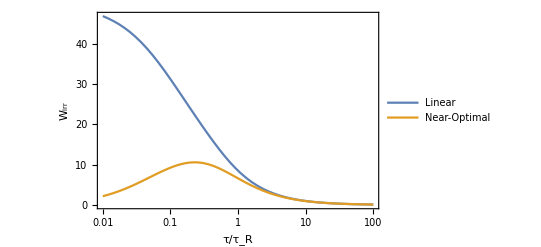

```mathematica
γ=10;
ω0=10;
τP=0.1;

LogLinearPlot[{Wirr[τ],Wirropt[τ]},{τ,0.01,100},Frame->True, FrameLabel->{"τ/τ_R","W_irr"},FrameStyle->Directive[Bold,Black,12],PlotLegends->Placed[{"Linear","Near-Optimal"},{Scaled[0.8],Scaled[0.8]}]]

Clear[γ,ω0,τP]
```

```mathematica
Wirr[τ_]=Assuming[{γ>0,ω0>0,τP>0},Integrate[Psi[t-u],{t,0,τ},{u,0,t}]]
```

$Aborted